Зад.1 Да се реши линейната система:

	a +  b - 2c +  d + 3e -  f       =    4
           2a -  b +  c + 2d +  e - 3f     =   20
    	a + 3b - 3c -  d + 2e +  f      =  -15
   	5a + 2b -  c -  d + 2e +  f     =    -3
  	-3a -  b + 2c + 3d +  e + 3f  =   16
    	4a + 3b +  c - 6d - 3e - 2f    =  -27

```mathematica
Solve[{a+b-2c+d+3e-f== 4,
2a-b+c+2d+e-3f== 20,
a+3b-3c-d+2e+f== -15,
5a+2b-c-d+2e+f== -3,
-3a-b+2c+3d+e+3f== 16,
4a+3b+c-6d-3e-2f== -27},{a,b,c,d,e,f}]
```

{{a→1,b→-2,c→3,d→4,e→2,f→-1}}

Зад.2 Да се намерят всички реални корени на уравненията
a)  x^4 = e^x;
б) 10 е^(-0,1 x^2) = √(2 π+ x)+ sin(2x).

```mathematica
NSolve[x^4==Exp[x],x,Reals]
```

{{x→-0.815553},{x→1.42961},{x→8.61317}}

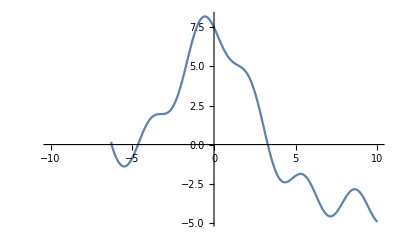

```mathematica
Plot[10 E^(-0.1 x^2)== √(2π+x)+Sin[2x],{x,-10,10}]
```

```mathematica
FindRoot[10 E^(-0.1 x^2)== √(2π+x)+Sin[2x],{x,-5}]
```

{x→-4.64893}

```mathematica
FindRoot[10 E^(-0.1 x^2)== √(2π+x)+Sin[2x],{x,-6}](*Коефициентът пред имагинерната единица е по-малък от машинната точност - можем да го считаме за 0*)
```

{x→-6.25999+1.73997×10^-18 ⅈ}

```mathematica
FindRoot[10 E^(-0.1 x^2)== √(2π+x)+Sin[2x],{x,3}]
```

{x→3.29029}

Зад.4  Като се използва x_0=0  за начално приближение,  да се намери числено корен на уравнението

2 + x^3-x-sin x = 0
 
Да се обяснят получените резултати. Да се намерят всички реални корени на уравнението с 15 значещи цифри.

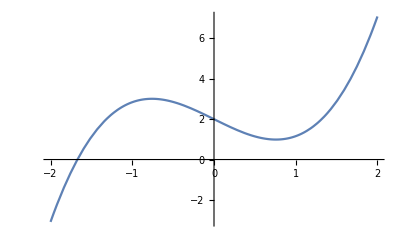

```mathematica
Plot[2+x^3-x-Sin[x]==0,{x,-2,2}]
```

```mathematica
FindRoot[2+x^3-x-Sin[x]==0,{x,0}] (*Започвайки търсенето от 0 и следвайки посоката на намаляване на функцията, алгоритъмът достига до локален минимум, вместо до действителния корен.*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→0.758482}

```mathematica
FindRoot[2+x^3-x-Sin[x]==0,{x,-2}]
```

{x→-1.67102}